```mathematica
legendreSymbol[a_Integer,p_Integer] := Module[{foo =PowerMod[a,(p-1)/2,p]} , If[foo==p-1 & p > 2,-1,foo]]
```

```mathematica
PrimeQ[50]
```

False

```mathematica
legendreSymbol[6,Prime[50]]
```

-1

```mathematica
foo = Select[Range[Prime[50]], legendreSymbol[#,Prime[50]]== 1&]
```

{1,3,4,5,9,11,12,14,15,16,17,19,20,25,26,27,33,36,37,42,43,44,45,46,48,49,51,53,55,56,57,58,60,61,62,64,68,70,71,75,76,78,80,81,82,83,85,91,94,95,97,99,100,103,104,108,111,118,121,125,126,129,130,132,134,135,138,144,146,147,148,149,151,153,154,158,159,161,165,167,168,169,171,172,173,174,176,178,180,181,183,184,185,186,187,192,193,196,202,203,204,209,210,212,213,214,215,217,218,220,224,225,226,228}

```mathematica
bar = Select[Range[Prime[50]],legendreSymbol[#,Prime[50]]== -1&]
```

{2,6,7,8,10,13,18,21,22,23,24,28,29,30,31,32,34,35,38,39,40,41,47,50,52,54,59,63,65,66,67,69,72,73,74,77,79,84,86,87,88,89,90,92,93,96,98,101,102,105,106,107,109,110,112,113,114,115,116,117,119,120,122,123,124,127,128,131,133,136,137,139,140,141,142,143,145,150,152,155,156,157,160,162,163,164,166,170,175,177,179,182,188,189,190,191,194,195,197,198,199,200,201,205,206,207,208,211,216,219,221,222,223,227}

```mathematica
Length[foo]
```

114

```mathematica
Length[bar]
```

114

The number of quadratic residues is the same as the number of non-residues.

```mathematica
legendreSum[a_Integer,p_Integer] := Sum[legendreSymbol[i,p],{i,1,a-1}]
```

```mathematica
legendreSum[Prime[100],Prime[100]]
```

0

```mathematica
legendreSum[Prime[1000],Prime[1000]]
```

0

```mathematica
legendreSum[Prime[10000],Prime[10000]]
```

0

legendreSum[a,a] = 0. The plot of the legendre sum is "even" or "odd" depending on whether p is 1 or 3 mod 4.

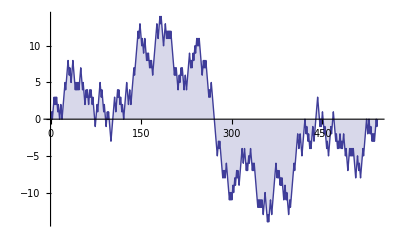

```mathematica
DiscretePlot[legendreSum[i,Prime[100]],{i,1,Prime[100]}]
```

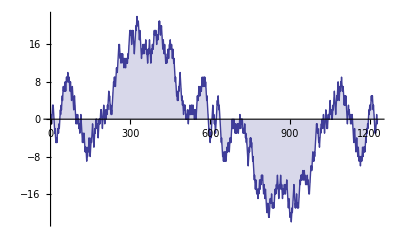

```mathematica
DiscretePlot[legendreSum[i,Prime[201]],{i,1,Prime[201]}]
```

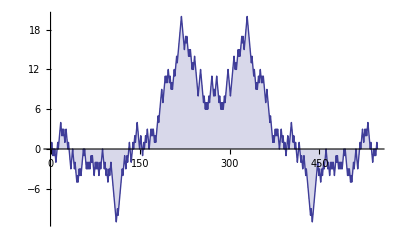

```mathematica
DiscretePlot[legendreSum[i,Prime[101]],{i,1,Prime[101]}]
```

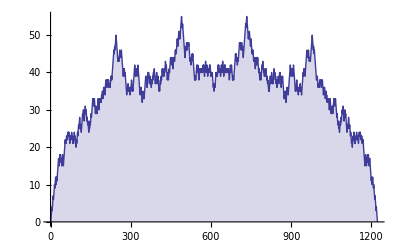

```mathematica
DiscretePlot[legendreSum[i,Prime[200]],{i,1,Prime[200]}]
```

```mathematica
gaussList[a_Integer,p_Integer?PrimeQ] :=Table[If[Mod[(a*i),p]> p/2, 1,0],{i,1,(p-1)/2}]
```

```mathematica
gaussPower[a_Integer,p_Integer?PrimeQ] := (-1)^(Plus @@gaussList[a,p])
```

```mathematica
Column[Map[Table[{i,#,gaussPower[i,#], legendreSymbol[i,#]}, {i,1,#-1}]&,Table[Prime[i],{i,2,10}]]]
```

{{1,3,1,1},{2,3,-1,-1}}
{{1,5,1,1},{2,5,-1,-1},{3,5,-1,-1},{4,5,1,1}}
{{1,7,1,1},{2,7,1,1},{3,7,-1,-1},{4,7,1,1},{5,7,-1,-1},{6,7,-1,-1}}
{{1,11,1,1},{2,11,-1,-1},{3,11,1,1},{4,11,1,1},{5,11,1,1},{6,11,-1,-1},{7,11,-1,-1},{8,11,-1,-1},{9,11,1,1},{10,11,-1,-1}}
{{1,13,1,1},{2,13,-1,-1},{3,13,1,1},{4,13,1,1},{5,13,-1,-1},{6,13,-1,-1},{7,13,-1,-1},{8,13,-1,-1},{9,13,1,1},{10,13,1,1},{11,13,-1,-1},{12,13,1,1}}
{{1,17,1,1},{2,17,1,1},{3,17,-1,-1},{4,17,1,1},{5,17,-1,-1},{6,17,-1,-1},{7,17,-1,-1},{8,17,1,1},{9,17,1,1},{10,17,-1,-1},{11,17,-1,-1},{12,17,-1,-1},{13,17,1,1},{14,17,-1,-1},{15,17,1,1},{16,17,1,1}}
{{1,19,1,1},{2,19,-1,-1},{3,19,-1,-1},{4,19,1,1},{5,19,1,1},{6,19,1,1},{7,19,1,1},{8,19,-1,-1},{9,19,1,1},{10,19,-1,-1},{11,19,1,1},{12,19,-1,-1},{13,19,-1,-1},{14,19,-1,-1},{15,19,-1,-1},{16,19,1,1},{17,19,1,1},{18,19,-1,-1}}
{{1,23,1,1},{2,23,1,1},{3,23,1,1},{4,23,1,1},{5,23,-1,-1},{6,23,1,1},{7,23,-1,-1},{8,23,1,1},{9,23,1,1},{10,23,-1,-1},{11,23,-1,-1},{12,23,1,1},{13,23,1,1},{14,23,-1,-1},{15,23,-1,-1},{16,23,1,1},{17,23,-1,-1},{18,23,1,1},{19,23,-1,-1},{20,23,-1,-1},{21,23,-1,-1},{22,23,-1,-1}}
{{1,29,1,1},{2,29,-1,-1},{3,29,-1,-1},{4,29,1,1},{5,29,1,1},{6,29,1,1},{7,29,1,1},{8,29,-1,-1},{9,29,1,1},{10,29,-1,-1},{11,29,-1,-1},{12,29,-1,-1},{13,29,1,1},{14,29,-1,-1},{15,29,-1,-1},{16,29,1,1},{17,29,-1,-1},{18,29,-1,-1},{19,29,-1,-1},{20,29,1,1},{21,29,-1,-1},{22,29,1,1},{23,29,1,1},{24,29,1,1},{25,29,1,1},{26,29,-1,-1},{27,29,-1,-1},{28,29,1,1}}

GaussPower is always equal to LegendreSymbol for any odd prime.

```mathematica
foo[a_] := Map[{a,#}&, Select[Range[3,a-1],PrimeQ]]
```

```mathematica
oplist = Join @@ Map[foo[#]&,Select[Range[3,1000],PrimeQ]];
```

```mathematica
leglist  = Map[legendreSymbol[#[[1]],#[[2]]]&, oplist];
```

```mathematica
revoplist = Map[{#[[2]], #[[1]]}&, oplist];
```

```mathematica
oplist
```

```mathematica
revoplist
```

{{3,5},{3,7},{5,7},{3,11},{5,11},{7,11},{3,13},{5,13},{7,13},{11,13},{3,17},{5,17},{7,17},{11,17},{13,17},«13831»,{883,997},{887,997},{907,997},{911,997},{919,997},{929,997},{937,997},{941,997},{947,997},{953,997},{967,997},{971,997},{977,997},{983,997},{991,997}}

```mathematica
quadRecip[p_Integer?PrimeQ, q_Integer?PrimeQ] := legendreSymbol[p,q]*(-1)^((p-1)(q-1)/4)
```

```mathematica
qrlist = Map[quadRecip[#[[1]],#[[2]]]&, revoplist];
```

```mathematica
qrlist == leglist
```

True

The program is stating that p is a square mod q iff q is a square mod 4, unless both p and q are equivalent to 3 mod 4, in which case p is a square mod q iss q is not a square mod 4.

```mathematica
Table[Mod[x^2,5],{x,1,4}]
```

{1,4,4,1}

5 is a quadratic residue for all odd primes which are equivalent to either 1 or 4 mod 5.

```mathematica
foo = Select[Range[3,10000],PrimeQ[#]&&legendreSymbol[6,#]==1&];
```

```mathematica
bar = Select[Range[3,10000], PrimeQ[#] && legendreSymbol[2,#] *legendreSymbol[3,#]==1&];
```

```mathematica
foo == bar
```

True

6 is a square mod p if either both 2 and 3 are square mod p or if neither 2 nor 3 are squares mod p.